```mathematica
CloseKernels[]
```

{KernelObject[13,local,<defunct>],KernelObject[14,local,<defunct>],KernelObject[15,local,<defunct>],KernelObject[16,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
e=1;
m=4;
P=2^m;
Ep=3000;
Dynamic[{Ep,e,t}]
```

```mathematica
ParallelTable[(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=1280-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=300;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
c=Table[10*Price⟦1⟧,{i,1,n}];
NStock=Table[0,{i,1,n},{i,1,2}];
W=Table[10*Price⟦1⟧,{i,1,n}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
"initial set";
AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,
Do[W⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[c⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[NStock⟦i,2⟧=0,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];];
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
N[{W⟦1⟧,W⟦2⟧,W⟦3⟧}]),{e,1,Ep}]//AbsoluteTiming
```

{26.03649,{{87.0658,3.18412},{32.3387,1.99007},{-33.5328,1.99007},{-14.428,0.398015},{25.1744,2.98511},{12.04,4.77618},{15.8211,7.16427},{8.0598,0.995037},{12.836,1.99007},{-0.0995037,1.79107},{49.4533,2.5871},{10.4479,1.39305},{-13.234,0.79603},{-85.0757,2.18908},{-11.4429,5.97022},{-40.1,2.38809},{19.8012,1.79107},{36.7169,1.19404},{-7.86079,2.5871},{18.0102,1.79107}}}

```mathematica
K=%⟦2⟧
```

{{87.0658,3.18412},{32.3387,1.99007},{-33.5328,1.99007},{-14.428,0.398015},{25.1744,2.98511},{12.04,4.77618},{15.8211,7.16427},{8.0598,0.995037},{12.836,1.99007},{-0.0995037,1.79107},{49.4533,2.5871},{10.4479,1.39305},{-13.234,0.79603},{-85.0757,2.18908},{-11.4429,5.97022},{-40.1,2.38809},{19.8012,1.79107},{36.7169,1.19404},{-7.86079,2.5871},{18.0102,1.79107}}

```mathematica
K⟦All,1⟧
```

{87.0658,32.3387,-33.5328,-14.428,25.1744,12.04,15.8211,8.0598,12.836,-0.0995037,49.4533,10.4479,-13.234,-85.0757,-11.4429,-40.1,19.8012,36.7169,-7.86079,18.0102}

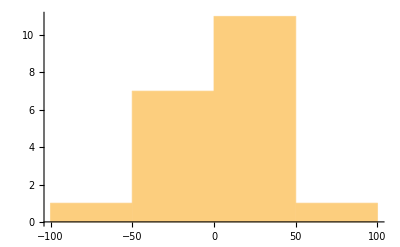

```mathematica
Histogram[K⟦All,1⟧]
```

```mathematica
Dimensions[K]⟦1⟧
```

100

```mathematica
KK=Table[{K⟦i,2⟧,(K⟦i,1⟧*n)},{i,1,Dimensions[K]⟦1⟧}];
```

```mathematica
KK
```

{{70.0506,22205.3},{54.329,12340.},{30.6471,2406.1},{27.065,1538.23},{17.9107,-390.751},{32.8362,3093.87},{63.6824,18059.8},{23.6819,646.476},{19.3037,-212.838},{23.2839,457.021},{66.2695,19627.6},{4.17916,-2401.12},{4.97519,-2337.64},{40.5975,6250.72},{4.17916,-2020.02},{27.264,1555.54},{101.892,50036.5},{24.4779,765.88},{70.4486,22828.},{24.2789,830.956},{12.3385,-1632.16},{1.79107,-2425.01},{53.533,11990.5},{19.5027,-771.452},{39.0055,5340.86},{30.8462,2622.02},{27.264,1129.47},{2.5871,-2532.87},{19.1047,-379.408},{44.9757,7915.62},{11.7414,-1444.1},{5.77122,-2013.26},{37.2144,4554.19},{8.95533,-1668.18},{104.081,51770.1},{26.269,1090.66},{26.866,1449.27},{4.97519,-2005.5},{68.4586,20898.1},{20.8958,95.6231},{50.7469,11069.7},{86.5682,35165.9},{3.38313,-1836.54},{5.97022,-2268.39},{3.78114,-2228.78},{68.8566,21370.1},{56.3191,13392.7},{38.8065,5105.83},{51.3439,11243.},{45.1747,7961.59},{84.7772,33918.9},{77.6129,28244.8},{54.9261,12816.6},{60.6973,15827.2},{46.1697,8676.23},{48.5578,9625.49},{32.6372,2830.98},{10.7464,-1539.82},{24.0799,461.399},{11.3434,-1383.6},{100.101,47842.9},{14.1295,-1458.43},{30.6471,2387.39},{25.2739,988.768},{25.0749,963.296},{31.8412,2547.99},{43.3836,7456.51},{50.5479,10347.3},{56.5181,14382.6},{56.5181,13807.},{58.7072,14893.8},{26.468,1043.89},{1.39305,-2044.5},{31.8412,2790.78},{25.0749,914.539},{19.7017,-25.9705},{4.17916,-2345.4},{67.4635,20791.8},{50.5479,11154.7},{32.8362,3147.4},{52.936,11455.},{23.0849,54.6275},{45.5727,7686.96},{30.6471,2466.},{7.36328,-1776.44},{0.995037,-2216.45},{24.2789,776.428},{55.3241,12838.3},{67.4635,20563.3},{26.468,1315.94},{31.8412,2646.5},{25.2739,640.107},{32.6372,3148.4},{76.8169,26805.4},{30.4481,2491.67},{57.9112,14715.1},{1.59206,-2524.71},{43.9806,7386.86},{12.7365,-1172.45},{35.2243,3686.31}}

```mathematica
"|Δp(T,1)|"
```

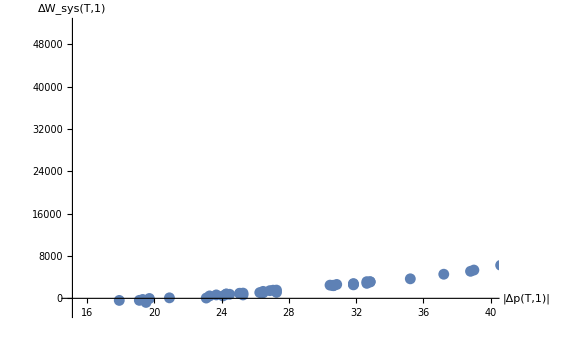

```mathematica
ListPlot[KK,AxesLabel->{"|Δp(T,1)|","ΔW_sys(T,1)"},PlotRange->{{15,40},All}]
```

```mathematica
Export["C:\\Users\\Jack\\Desktop\\LabWork\\final\\openm6s2p100T1279.txt",Compress[re⟦2⟧]]
```

C:\Users\Jack\Desktop\LabWork\final\openm6s2p100T1279.txt

```mathematica
Walll=Uncompress[ReadList["C:\\Users\\Jack\\Desktop\\LabWork\\final\\openm6s2T1279PRICE300REAL3000.txt",String]⟦1⟧];
```

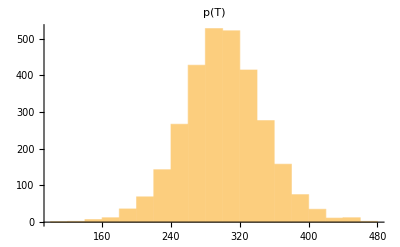

```mathematica
Histogram[N[Walll⟦All,4⟧],PlotLabel->"p(T)"]
```

```mathematica
Walll⟦All,1⟧
```

{3000+36/(√101)-√101,3000+16/(√101)+√101,3000-20/(√101)-√101,3000-73/(√101),3000+32/(√101)-√101,3000-78/(√101)-√101,3000-56/(√101)+√101,2987,3000-77/(√101),3000-25/(√101),3000+74/(√101)-√101,3000-72/(√101)+√101,3000+25/(√101)+2 √101,3000-16/(√101)+√101}
 |  |  |  |

```mathematica
Ep=3000;
```

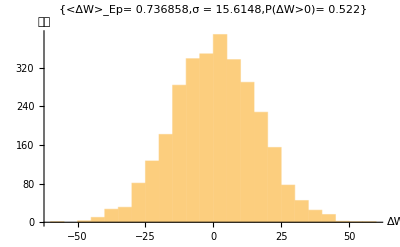

```mathematica
Histogram[Walll⟦All,1⟧-3000,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Walll⟦All,1⟧-3000]]],"σ = "<>ToString[N[StandardDeviation[Walll⟦All,1⟧-3000]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[Walll⟦All,1⟧-3000]],3]]}]
```

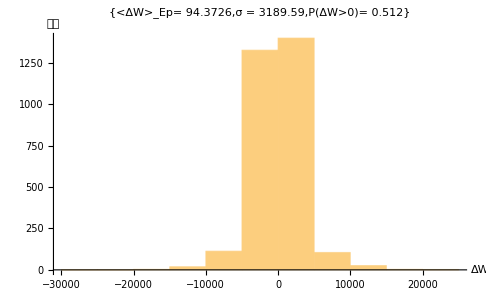

```mathematica
Histogram[Walll⟦All,2⟧-3000,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Walll⟦All,2⟧-3000]]],"σ = "<>ToString[N[StandardDeviation[Walll⟦All,2⟧-3000]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[Walll⟦All,2⟧-3000]],3]]}]
```

```mathematica
WA=Mean[N[Walll⟦All,3⟧-3000]]
WS=StandardDeviation[N[Walll⟦All,3⟧-3000]]
PW=N[1/Ep Total[UnitStep[N[Walll⟦All,3⟧-3000]]],3]
```

86.3365

174.064

0.627

86.3365

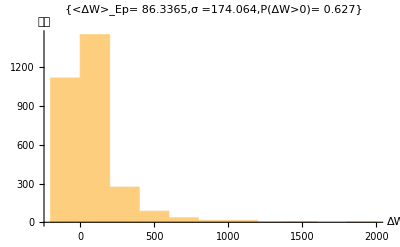

```mathematica
Histogram[N[Walll⟦All,3⟧-3000],AxesLabel->{ΔW,次數},PlotLabel->{{ "<ΔW>_Ep= "}<>ToString[WA],"σ ="<>ToString[WS],"P(ΔW>0)= "<>ToString[PW]}]
```

```mathematica
Histogram[N[Walll⟦All,3⟧-3000],AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Walll⟦All,3⟧-3000]]],"σ = "<>ToString[N[StandardDeviation[Walll⟦All,3⟧-3000]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[Walll⟦All,3⟧-3000]],3]]}]
```

$Aborted

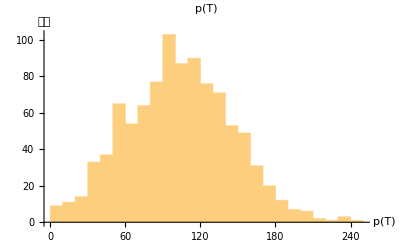

```mathematica
Histogram[Wall⟦4⟧,AxesLabel->{"p(T)",次數},PlotLabel-> "p(T)"]
```